```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

# Physics 449: Homework 4

## Srijyotsna Lucky Volety

## Question 1-2:

Defined in lecture notes:

B = (2 μ_B L)/r^3
H_SO=2 μ_B S·B
          = (2 μ_B^2 S·L)/r^2 
          = (2 S·L)/r^2 ((e ℏ)/(2m c))^2
ζ = (2 μ_B^2)/(r^2 a_B^3)=1/(2 r^2 a_B^3)((e ℏ)/(m c))^2
L·S=(J^2- L^2-S^2)/2=(j(j+1)-l(l+1)-s(s+1))/2=Piecewise[{{1/2, j=3/2}, {-1, j=1/2}}]

if H_SO=ζ S·L, then H_SO must be:
H_SO = 1/(2 r^2 a_B^3)((e ℏ)/(m c))^2 S·L
H = H_0+H_SO
H=ℏ^2/(m a^2)(-1/2∂_s^2 +((l(l+1))/(2 s^2)-1/s))+1/(2 s^2 a_B^3)((e ℏ)/(m c))^2 S·L

Scaling:
H=(-1/2∂_s^2 +((l(l+1))/(2 s^2)-1/s))+1/(2 s^3 a_B m)(e/c)^2 S·L
if H_a= e^2/a_B= ℏ^2/(m a_B^2)=α m c^2
α = e^2/ℏc=1/137
H=(-1/2∂_s^2 +((l(l+1))/(2 s^2)-1/s))+(α^2 mc^2)/(2 s^3 m)(1/c)^2 S·L
H=(-1/2∂_s^2 +((l(l+1))/(2 s^2)-1/s))+α^2/(2 s^3)S·L

Matrix Calculations:

```mathematica
Subscript[P, n_,l_,z_][r_]:=√z Subscript[P, n,l][z r]
```

```mathematica
n = Range[2,6];
```

```mathematica
Hso=Table[Integrate[Subscript[P, n1,1,1][r]Subscript[P, n2,1,1][r] 1/r^3,{r,0,∞}],{n1,n},{n2,n}]//FullSimplify
```

{{1/24,-8/375,7/(162 √10),-1096/(50421 √5),67/(1536 √35)},{-8/375,1/81,-(628 √(2/5))/50421,77/(6144 √5),-4456/(177147 √35)},{7/(162 √10),-(628 √(2/5))/50421,1/192,-(12508 √2)/4782969,24601/(2343750 √14)},{-1096/(50421 √5),77/(6144 √5),-(12508 √2)/4782969,1/375,-37814408/(7073843073 √7)},{67/(1536 √35),-4456/(177147 √35),24601/(2343750 √14),-37814408/(7073843073 √7),1/648}}

```mathematica
Hso//N//MatrixForm
```

(0.0416667 | -0.0213333 | 0.0136642 | -0.00972107 | 0.00737309
-0.0213333 | 0.0123457 | -0.00787731 | 0.00560473 | -0.00425184
0.0136642 | -0.00787731 | 0.00520833 | -0.00369833 | 0.00280529
-0.00972107 | 0.00560473 | -0.00369833 | 0.00266667 | -0.00202047
0.00737309 | -0.00425184 | 0.00280529 | -0.00202047 | 0.00154321)

```mathematica
En = -1/(2 n^2); α = 1/137;
```

For j = 1/2, L·S = -1:

```mathematica
H1 = DiagonalMatrix[En] - α^2/2 Hso//FullSimplify//N
```

{{-0.125001,5.68313×10^-7,-3.64009×10^-7,2.58966×10^-7,-1.96417×10^-7},{5.68313×10^-7,-0.0555559,2.09849×10^-7,-1.49308×10^-7,1.13268×10^-7},{-3.64009×10^-7,2.09849×10^-7,-0.0312501,9.85222×10^-8,-7.4732×10^-8},{2.58966×10^-7,-1.49308×10^-7,9.85222×10^-8,-0.0200001,5.38247×10^-8},{-1.96417×10^-7,1.13268×10^-7,-7.4732×10^-8,5.38247×10^-8,-0.0138889}}

```mathematica
H1//MatrixForm
```

(-0.125001 | 5.68313×10^-7 | -3.64009×10^-7 | 2.58966×10^-7 | -1.96417×10^-7
5.68313×10^-7 | -0.0555559 | 2.09849×10^-7 | -1.49308×10^-7 | 1.13268×10^-7
-3.64009×10^-7 | 2.09849×10^-7 | -0.0312501 | 9.85222×10^-8 | -7.4732×10^-8
2.58966×10^-7 | -1.49308×10^-7 | 9.85222×10^-8 | -0.0200001 | 5.38247×10^-8
-1.96417×10^-7 | 1.13268×10^-7 | -7.4732×10^-8 | 5.38247×10^-8 | -0.0138889)

```mathematica
eval1 = Eigenvalues[H1]
```

{-0.125001,-0.0555559,-0.0312501,-0.0200001,-0.0138889}

For j = 3/2, L·S = 1/2:

```mathematica
H2 = DiagonalMatrix[En] + α^2/4 Hso//FullSimplify//N
```

{{-0.124999,-2.84156×10^-7,1.82004×10^-7,-1.29483×10^-7,9.82084×10^-8},{-2.84156×10^-7,-0.0555554,-1.04925×10^-7,7.46541×10^-8,-5.66339×10^-8},{1.82004×10^-7,-1.04925×10^-7,-0.0312499,-4.92611×10^-8,3.7366×10^-8},{-1.29483×10^-7,7.46541×10^-8,-4.92611×10^-8,-0.02,-2.69124×10^-8},{9.82084×10^-8,-5.66339×10^-8,3.7366×10^-8,-2.69124×10^-8,-0.0138889}}

```mathematica
eval2 = Eigenvalues[H2]
```

{-0.124999,-0.0555554,-0.0312499,-0.02,-0.0138889}

2p P_(3/2)-2p P_(1/2) energy splitting:

```mathematica
eval2⟦1⟧-eval1⟦1⟧
```

1.66498×10^-6

compare to ⟨H_so⟩:

```mathematica
expHso=α^2/2 Hso⟦1,1⟧ *(1/2+1)//N
```

1.66498×10^-6

They match!

## Question 3: Townsend 11.1:

H_1=bx^4
H_0= p_x^2/(2m)+1/2 mω^2 x^2
x = x_0(a + a^†)  & x_0= √ℏ/(2mω)
H_0=ℏω(a a^†+1/2)
Using a a^†=n+1,a^†a=n, H_0 simplifies to:
H_0= ℏω(n + 1/2)
H_0 n=E_n^0 n
E_n^0=ℏω(n +1/2)

E_n^1= n H_1 n= n bx^4 n=b n x^4 n=(b(√ℏ/(2mω)))^4,⟨x^4⟩=b(√ℏ/(2mω))^4,⟨(a+a^†)^4⟩
=(b(√ℏ/(2mω)))^4⟨(a+a^†)(a+a^†)(a+a^†)(a+a^†)⟩=(b(√ℏ/(2mω)))^4⟨(a a+a a^†+a^†a+a^†a^†)(a a+a a^†+a^†a+a^†a^†)⟩
= (b(√ℏ/(2mω)))^4⟨a a a a+a a a a^†+a a a^†a +a a a^†a^†+a a^†a a+a a^†a a^†+a a^†a^†a+a a^†a^†a^†+a^†a a a+a^†a a a^†+a^†a a^†a+a^†a a^†a^†+a^†a^†a a+a^†a^†a a^†+a^†a^†a^†a+a^†a^†a^†a^†⟩
The only terms that remain will have two a & a^†:
= (b(√ℏ/(2mω)))^4⟨a a a^†a^†+a a^†a a^†+a a^†a^†a+a^†a a a^†+a^†a a^†a+a^†a^†a a⟩
= (b(√ℏ/(2mω)))^4⟨a a a^†a^†+a a^†a a^†+a a^†a^†a+a^†a a a^†+a^†a a^†a+a^†a^†a a⟩
=(b(√ℏ/(2mω)))^4(√(n+1)(n+2)√(n+1) +(n+1)(n+1)+(n+1) n+√n(n-1)√n+n n+n (n+1))

```mathematica
ClearAll[n];
```

```mathematica
En0 = ℏ ω(n +1/2);
```

```mathematica
En1=b(√ℏ/(2m ω))^4*(√(n+1)(n+2)√(n+1) +(n+1)(n+1)+(n+1) n+√n(n-1)√n+n n+n (n+1))//Simplify
```

(3 b (1+2 n+2 n^2) ℏ^2)/(4 m^2 ω^2)

Part B: even if b is very small, at large n perturbation expansion goes like this:

```mathematica
En1/En0//Simplify
```

(3 b (1+2 n+2 n^2) ℏ)/(2 m^2 (1+2 n) ω^3)

If b and non n-terms are negligible:

```mathematica
(1+2 n+2 n^2)/(1+2n)//FullSimplify
```

1/2+n+1/(2+4 n)

The 1/2 is negligible as well, 1/(2 +4n)→ 0, and all that will be left is n. So for large n, En1/En0 is proportional to n. And perturbation theory would not really work.

## Question 4: Townsend 11.5:

Given the Hamiltonian (11.7) & Revisited in 11.53, code used from Thad’s PT.nb:
H_1 =  (1H1 | 1H2
2H1 | 2H2)=(μE | A
A | -μE)

```mathematica
$Assumptions={A>0,μE>0};
```

```mathematica
{E0,kets}=Eigensystem[{{μE, A}, {A, -μE}}];
```

```mathematica
evec =Normalize/@kets//FullSimplify;
```

```mathematica
evecnorm = evec/. μE ->0//FullSimplify
```

{{-1/(√2),1/(√2)},{1/(√2),1/(√2)}}

```mathematica
ψ1 =evecnorm⟦1⟧+evecnorm⟦2⟧  (evecnorm⟦2⟧ .{{μE, 0}, {0, -μE}}.evecnorm⟦1⟧)/(-2A)
```

{-1/(√2)+μE/(2 √2 A),1/(√2)+μE/(2 √2 A)}

```mathematica
ψ2 =evecnorm⟦2⟧+evecnorm⟦1⟧  (evecnorm⟦1⟧ .{{μE, 0}, {0, -μE}}.evecnorm⟦2⟧)/(-2A)
```

{1/(√2)-μE/(2 √2 A),1/(√2)+μE/(2 √2 A)}

Part B:

```mathematica
Series[evec,{μE,0,1}]// PowerExpand//FullSimplify
```

{{-1/(√2)+μE/(2 √2 A)+O[μE]^2,1/(√2)+μE/(2 √2 A)+O[μE]^2},{1/(√2)+μE/(2 √2 A)+O[μE]^2,1/(√2)-μE/(2 (√2 A))+O[μE]^2}}

These also match!

## Question 5: Townsend 11.7:

V=Piecewise[{{-e^2/r, r>R}, {(-3 e^2)/(2R)+(e^2 r^2)/(2 R^3), r<R}}]
E_n^1=⟨V_1⟩

## Question 6:

According to Thad on piazza: (note m_j=g_j)
^2 D_j: 2 → (2s +1=l?)→ 2s+1 =2, D→d-state → l=2, need to find j.
So :   s = (+/-)1/2; l =2;
And the total angular momentum is therefore the sum of the spin and orbital angular momentum:
j=s+l=1/2+2=5/2   &  j =s+l=-1/2+2=3/2
m = 5/2 or 3/2
Knowing this, we can use Clebsch-Gordan to solve for the expectation value of J_z.
m_j⟨J_z⟩=⟨L_z+2 S_z⟩=m_j((⟨L·S⟩ + l(l+1)+2⟨L·S⟩+2s(s+1))/(j(j+1)))
m_j 5/2 = (2 + (1/2*2)) = (2+1)=3
m_j=6/5=g_i

For j = 5/2 & m=5/2:
Only one possible way for j & m to be 5/2, l=2 and s=1/2
j m_j=Cl s
5/2 5/2=C2 1/2
⟨L_z+2 S_z⟩=m_j((⟨L·S⟩ + l(l+1)+2⟨L·S⟩+2s(s+1))/(j(j+1)))
m_j 5/2 = (2 + (1/2*2)) =((C^jm_s)_(lm_l sm_s))^2 (3)=1*3=3
m_j=3*2/5=6/5=g_i
((⟨L·S⟩ + l(l+1)+2⟨L·S⟩+2s(s+1))/(j(j+1)))=((1+2(2+1)+2(1)+1(3/2))/(5/2(7/2)))

```mathematica
ClebschGordan[{2,2},{1/2,1/2},{5/2,5/2}]
```

1

```mathematica
((1+2(2+1)+2(1)+1(3/2))/(5/2(7/2)))//FullSimplify
```

6/5

So the g_(5/2) factor =6/5

For j=3/2&m=3/2:
There are two possible ways for j & m to be 3/2, l=2 and s=-1/2 or l=1, s=1/2 so the answer will be a combination of the two states.
m_j⟨J_z⟩=⟨L_z+2 S_z⟩=m_j((⟨L·S⟩ + l(l+1)+2⟨L·S⟩+2s(s+1))/(j(j+1)))
m_j 3/2 = (2 + (-1/2*2)) + (1+1)=((C^jm_s)_(lm_l sm_s))^2 (2)+((C^jm_s)_(lm_l sm_s))^2 (2-1)=(1/5)2 +(4/5)1 =6/5
m_j=2/3*6/5=12/15=4/5=g_i

j m_j=Cl s
3/2 3/2=C2-1/2+ C1 1/2

```mathematica
ClebschGordan[{2,1},{1/2,1/2},{3/2,3/2}]
ClebschGordan[{2,2},{1/2,-1/2},{3/2,3/2}]
```

-1/(√5)

2/(√5)

## Question 7:

Like in question 6, s = (+/-)1/2, l=2. Zeeman effect with magnetic field.

H_0=A S·I
V = 2 μ_B B ·S_z

You need a factor of 2/5 in the front of the Hso matrix (I think it's the energy difference 2/5=6/5-4/5)Rest of the code is following Thad's perturbation theory notebook

```mathematica
s=angmom[1/2];l=angmom[2];
Hso =2/5 Sum[l⟦p⟧⊗s⟦p⟧,{p,3}];
Htot=2/5 Sum[l⟦p⟧⊗s⟦p⟧,{p,3}]+μB A(l⟦3⟧⊗IdentityMatrix[2]+2IdentityMatrix[5]⊗s⟦3⟧);
```

```mathematica
eval = Eigenvalues[Hso]
```

{-3/5,-3/5,-3/5,-3/5,2/5,2/5,2/5,2/5,2/5,2/5}

```mathematica
{E0,kets}=Eigensystem[Htot];
kets=Normalize/@kets;
```

```mathematica
E0
```

{1/5 (2-15 A),1/5 (2+15 A),1/10 (-1-15 A-√5 √(5-6 A+5 A^2)),1/10 (-1-15 A+√5 √(5-6 A+5 A^2)),1/10 (-1-5 A-√5 √(5-2 A+5 A^2)),1/10 (-1-5 A+√5 √(5-2 A+5 A^2)),1/10 (-1+5 A-√5 √(5+2 A+5 A^2)),1/10 (-1+5 A+√5 √(5+2 A+5 A^2)),1/10 (-1+15 A-√5 √(5+6 A+5 A^2)),1/10 (-1+15 A+√5 √(5+6 A+5 A^2))}

```mathematica
μB =1;
```

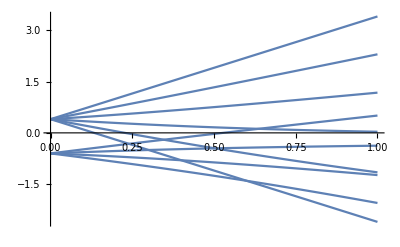

```mathematica
exact=Plot[Sort[E0],{A,0,1}]
```

Can see the y-intercepts of the values are at 2/5 &-3/5. We can isolate the different states from question 6 using the g factor and the j,m values found previously.

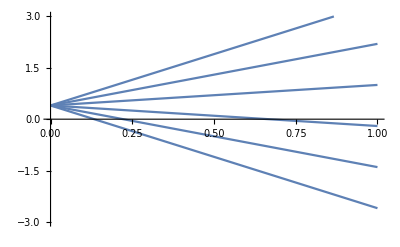

```mathematica
D52=Plot[2/5+(6/5) A*Range[-5/2,5/2],{A,0,1},PlotRange->{{0,1},{-3,3}}]
```

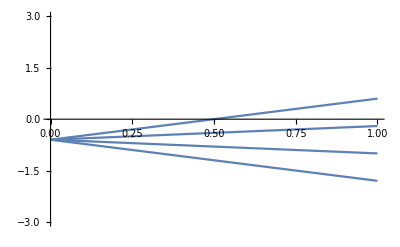

```mathematica
D32=Plot[-3/5+(4/5) A*Range[-3/2,3/2],{A,0,1},PlotRange->{{0,1},{-3,3}}]
```

A=(μ B)/E_so=B/(8.72 Gauss)(x-axis)    & E/(h*12.2 MHz) (y-axis)